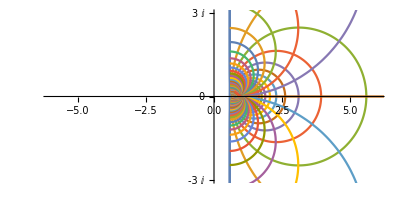

```mathematica
Show[ParametricPlot[Evaluate[Table[Tooltip[{Re[Zeta[a+I*b]],Im[Zeta[a+I*b]]},Row[{"a == ",a}]],{a,1,6,0.1}]],{b,-5,5},PlotRange->{{-6,6},{-3,3}},Ticks->{Automatic,{{-3,-3I},{-2,},{-1,},{0,0},{1,},{2,},{3,3I}}}],ParametricPlot[Evaluate[Table[Tooltip[{Re[Zeta[a+I*b]],Im[Zeta[a+I*b]]},Row[{"b == ",b ,I}]],{b,-5,5,0.1}]],{a,1,6},PlotRange->{{-6,6},{-3,3}}]
(*ParametricPlot[Evaluate[Table[Tooltip[{Re[Zeta[a+I*b]],Im[Zeta[a+I*b]]},Row[{"a == ",a}]],{a,-6,1,0.1}]],{b,-5,5},PlotRange->{{-6,6},{-3,3}},PlotStyle->Gray,Ticks->{Automatic,{{-3,-3I},{-2,},{-1,},{0,0},{1,},{2,},{3,3I}}}],ParametricPlot[Evaluate[Table[Tooltip[{Re[Zeta[a+I*b]],Im[Zeta[a+I*b]]},Row[{"b == ",b ,I}]],{b,-5,5,0.1}]],{a,-6,1},PlotRange->{{-6,6},{-3,3}},PlotStyle->Gray]*)]
```

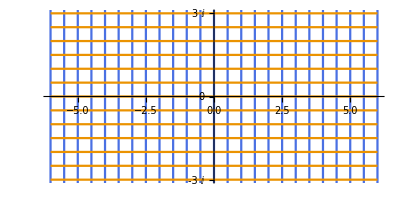

```mathematica
Show[ParametricPlot[Evaluate[Table[Tooltip[{a,b},Row[{"a == ",a}]],{a,-6,6,0.5}]],{b,-5,5},PlotRange->{{-6,6},{-3,3}},PlotStyle->ColorData["Atoms"]["N"],Ticks->{Automatic,{{-3,-3I},{-2,},{-1,},{0,0},{1,},{2,},{3,3I}}}],ParametricPlot[Evaluate[Table[Tooltip[{a,b},Row[{"b == ",b ,I}]],{b,-5,5,0.5}]],{a,-6,6},PlotStyle->ColorData["GeologicAges"]["Paleocene"],PlotRange->{{-6,6},{-3,3}}]]
```

```mathematica
Zeta[-1]
```

-1/12

```mathematica
Manipulate[ParametricPlot[{(1-x)Re[Zeta[a+I*b]],(1-x)Im[Zeta[a+I*b]]},{b,-5,5},{a,-6,6},PlotRange->{{-6,6},{-3,3}},Mesh->20],{x,0,1}]
```